```mathematica
Infinite Potential Well
```

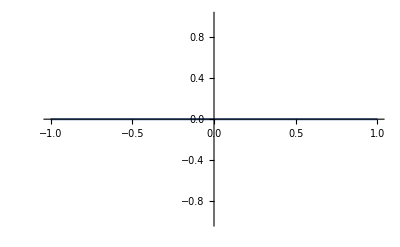

```mathematica
μ=1.0;
min=-1;max=1;step=500;
d=(max-min)/step;
V=Table[0,{x,Range[min,max,d]}];
ListLinePlot[V,PlotRange->All,DataRange->{min,max}]
```

```mathematica
En=4*1.24;
f=2(V-En);
```

```mathematica
u=ConstantArray[0,step];
g=ConstantArray[0,step];
u[[2]]=1;(*boundary conditions*)
g[[2]]=u[[2]](1-(d^2 f[[2]])/12);
g[[1]]=u[[1]](1-(d^2 f[[1]])/12);
(*g[[step]]=u[[step]](1-(d^2 f[[step]])/12);*)
```

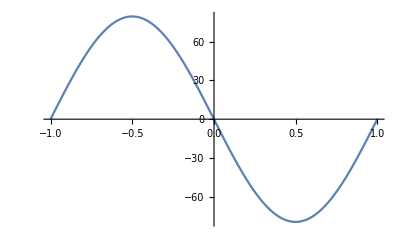

```mathematica
Do[g[[i+1]]=2 g[[i]]-g[[i-1]]+d^2 f [[i]]u[[i]];u[[i+1]]=g[[i+1]]/(1-(d^2 f[[i+1]])/12),{i,2,step-1,1}]
ListLinePlot[g,PlotRange->All,DataRange->{min,max}]
```